# Linear Regression

Linear regression is used to model the  relationship between two variables by fitting a linear equation to the observed data.

## Connection to Correlation

When we conclude there is a linear correlation between two variables, we can then proceed to find the regression equation. This is the equation of the straight line that best fits the data in a scatter diagram.

Regression equation
						ŷ = b_0 + b_1x

where x is the predictor variable, ŷ is the response variable, b_0 is the y-intercept, and b_1 is the slope.

In the previous example, when we analyzed data from the Anorexia Treatment facility. We noticed that there was no correlation for starting and ending weights in the control group, we showed that in the behavioral treatment group the entry and exit weights were correlated, and although the correlation test showed some correlation, the data does pass the normality test.

Loading data

```mathematica
dataAnrx=ResourceData["Sample Data: Anorexia Treatment"];
```

Separating the three different groups in the study

```mathematica
controlData=dataAnrx[Select[#Treatment == "Cont" &]];
btreatmentData=dataAnrx[Select[MatchQ[#Treatment ,Alternatives["CBT"]]&]];
ftreatmentData=dataAnrx[Select[MatchQ[#Treatment ,Alternatives["FT"]]&]];
```

Obtaining the Linear Regression Equation of Each Group

```mathematica
model1=LinearModelFit[Values@QuantityMagnitude@Normal@controlData[All,{"EntryWeight","ExitWeight"}],x,x];
model1["BestFit"]
model2=LinearModelFit[Values@QuantityMagnitude@Normal@btreatmentData[All,{"EntryWeight","ExitWeight"}],x,x];
model2["BestFit"]
model3=LinearModelFit[Values@QuantityMagnitude@Normal@ftreatmentData[All,{"EntryWeight","ExitWeight"}],x,x];
model3["BestFit"]
```

92.0515-0.134185 x

15.5772+0.847982 x

14.8198+0.909226 x

Plotting the data points and line of best fit

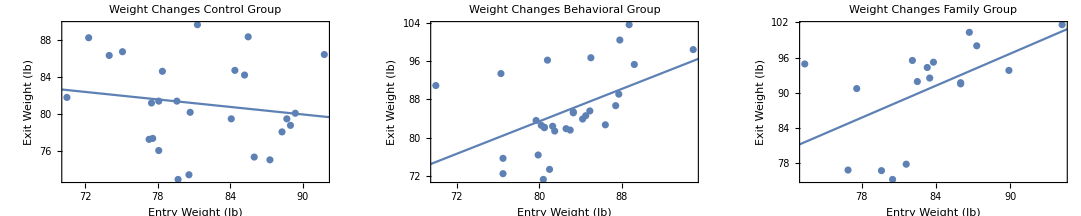

```mathematica
GraphicsGrid[{{Show[ListPlot[controlData[All,{"EntryWeight","ExitWeight"}]],Plot[model1["BestFit"],{x,0,100}],PlotLabel->Style["Weight Changes Control Group",12],Frame->True,FrameLabel->{"Entry Weight (lb)","Exit Weight (lb)"}],Show[ListPlot[btreatmentData[All,{"EntryWeight","ExitWeight"}]],Plot[model2["BestFit"],{x,0,100}],PlotLabel->Style["Weight Changes Behavioral Group",12],Frame->True,FrameLabel->{"Entry Weight (lb)","Exit Weight (lb)"}],Show[ListPlot[ftreatmentData[All,{"EntryWeight","ExitWeight"}]],Plot[model3["BestFit"],{x,0,100}],PlotLabel->Style["Weight Changes Family Group",12],Frame->True,FrameLabel->{"Entry Weight (lb)","Exit Weight (lb)"}]}},Frame->All,AspectRatio->Automatic]
```

### Residuals and the Least Squares Properties

The straight line that best fits the data is based of the vertical distances between the original data points and the regression line, these distances are called residuals.
To find the line of best fit for the data we’ve used thus far, we can try using the demonstration below and we need to find the line that gives us smallest value of the sum of the squares. You can change the slope and the y-intercept of the equation, and if you do give up, you can just click on the tab “show least squares line”.
You will notice that the line with smallest sum of squares is the line of best fit we showed in the above graphs.

```mathematica
squaredResidualPlot[data_List, int_?NumberQ, 
slope_?NumberQ, opts___Rule]:=Module[{x,xdata,ydata,line,pred,resid,i,l,p,redEdges,squares,dashedEdges},xdata=data[[All,1]];ydata=data[[All,2]];
line=int + slope*x;
If[slope==0,pred=Table[int,{i,Length[xdata]}], pred=line /. x->xdata];
resid=If[slope>0, ydata-pred, pred-ydata];
l=ListPlot[data, opts,AxesOrigin->{0,0},PlotRange->{{70,95},{70,95}},PlotStyle->AbsolutePointSize[4]];
p=Plot[line, {x,0,100},opts,PlotStyle->{Hue[.7]}];
redEdges=Prepend[MapThread[Line[{{#1,#3},{#1-#4,#3},{#1-#4,#2},{#1,#2}}]&,{xdata,ydata,pred,resid}],Hue[1]];
squares=Prepend[MapThread[Rectangle[{#1-#4,#3},{#1,#2}]&,{xdata,ydata,pred,resid}],Opacity[.2]];
dashedEdges=Prepend[MapThread[Line[{{#1,#2},{#1,#3}}]&,{xdata,ydata,pred}],Dashing[{.01}]];
Show[l,p,Graphics[squares],Graphics[redEdges],Graphics[dashedEdges],AspectRatio->Automatic,AxesLabel->{"x", "y"},PlotLabel->"sum of squares: "<>ToString[PaddedForm[Plus@@(resid^2),{6,3}]]]
]
data1=Values@QuantityMagnitude@Normal@controlData[All,{"EntryWeight","ExitWeight"}];
data2=Values@QuantityMagnitude@Normal@btreatmentData[All,{"EntryWeight","ExitWeight"}];
data3=Values@QuantityMagnitude@Normal@ftreatmentData[All,{"EntryWeight","ExitWeight"}];
{{m1,b1},{m2,b2},{m3,b3}}={Coefficient[#,x],Coefficient[#,x,0]}&/@(Fit[#,{1,x},x]&/@{data1,data2,data3});Manipulate[
Column[{
squaredResidualPlot[data,b,m,ImageSize->{600,400}],
Button["show least squares line",
Which[
data===data1,m=m1;b=b1,
data===data2,m=m2;b=b2,
data===data3,m=m3;b=b3]]
}],
{{data,data1},{data1->"control",data2->"behavioral",data3->"family"}},
{{m,.9,"slope"},-1.5,1.5},
{{b,1,"intercept"},10,95},
SaveDefinitions->True,AutorunSequencing->{3,2}]
```

Summary of sum of square for each group

```mathematica
Text[Grid[{{"Group","Sum of Squares"},{"Control",Total[model1["FitResiduals"]^2]},{"Behavioral",Total[model2["FitResiduals"]^2]},{"Family",Total[model3["FitResiduals"]^2]}},Alignment->{{Left,Left},{"Center,Center"}},Dividers->Center,Background->{None,{Yellow,None}}]]
```

Group | Sum of Squares
Control | 548.037
Behavioral | 1480.41
Family | 816.341

#### Residual Plots

A residual plot is simply a scatter plot of the (x,y) values after each of the y coordinates has been replaced by the residual value y-ŷ. The coordinates are of the points are (x,  y-ŷ).

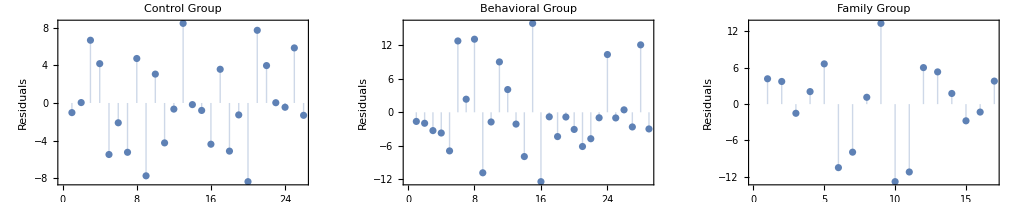

```mathematica
GraphicsGrid[{{ListPlot[model1["FitResiduals"],Frame->True,FrameLabel->{None,"Residuals"},Filling->Axis,PlotLabel->Style["Control Group",12]],ListPlot[model2["FitResiduals"],Frame->True,FrameLabel->{None,"Residuals"},Filling->Axis,PlotLabel->Style["Behavioral Group",12]],ListPlot[model3["FitResiduals"],Frame->True,FrameLabel->{None,"Residuals"},Filling->Axis,PlotLabel->Style["Family Group",12]]}},Frame->False,AspectRatio->Automatic]
```

Further Explorations

Multiple Correlation

Authorship information

Silvani Vejar

07/04/2017

E.Vejar@northeastern.edu

References
“Least Squares Criteria for the Least Squares Regression Line” from the Wolfram Demonstrations Project
 http://demonstrations.wolfram.com/LeastSquaresCriteriaForTheLeastSquaresRegressionLine/
Contributed by: Mariel Maughan and Bruce Torrence
Based on a program by: Bruce Torrence
Understandable Statistics by Brase and Brase